## init

Set the library’s directory first!

```mathematica
directory="/home/tchr/Projects/Mathematica/MSE-Mathematica/";
```

```mathematica
Get["mse.m",Path->directory];
```

## Import precomputed data

Set the data’s directory preferably in the variable ‘filename’.

```mathematica
filename=directory<>"import/"<>"round1m1-1.xls.pre.dat";
```

Load the data in variables with meaningful names

```mathematica
{header,noM,noU,noD,noAttr,distanceMatrices,matchMatrix,mate}=import[filename,"precomp"];
```

## Routines (calculate payoff matrix, inequalities members, dataArray)

```mathematica
payoffMatrix=CpayoffMatrix[payoffDM,noM,noU,noD];
```

```mathematica
ineqmembers=Cineqmembers[mate];
```

```mathematica
dataArray=CdataArray[payoffMatrix,Cx[noAttr-1]];
```

## Maximization

The global variable “permuteinvariant” when set to true the order of the attributes is set related to their statistics.

```mathematica
permuteinvariant=True;
```

### Differential Evolution Method

The default DifferentialEvolution parameters:

option name | default value |  
"CrossProbability" | 0.5 | probability that a gene is taken from x_i
"InitialPoints" | Automatic | set of initial points 
"PenaltyFunction" | Automatic | function applied to constraints to penalize invalid points
"PostProcess" | Automatic | whether to post-process using local search methods 
"RandomSeed" | 0 | starting value for the random number generator
"ScalingFactor" | 0.6 | scale applied to the difference vector in creating a mate 
"SearchPoints" | Automatic | size of the population used for evolution 
"Tolerance" | 0.001 | tolerance for accepting constraint violations

```mathematica
?maximize
```

maximize[dataArray_,noAttr_,method_:"DifferentialEvolution",permuteinvariant_:False,printflag_:False] is MSE specific and uses the optimize function. It uses objective function (that counts the number of satisfied inequalities). It returns a list {max,{x1->value1, x2->value2, ...}} where max is the maximum number of satisfied inequalities found and the solution {x1,x2,...}

```mathematica
method1={"DifferentialEvolution","CrossProbability"->0.5,"InitialPoints"->Automatic,"PenaltyFunction"->Automatic,"PostProcess"->Automatic,"RandomSeed"->0,"ScalingFactor"->0.6,"SearchPoints"->Automatic,"Tolerance"->0.001};
sol1=maximize[dataArray,noAttr,method1,permuteinvariant,True];
```

order={2,1}  reverse order={3.18803,2.22377}

Method {DifferentialEvolution, CrossProbability -> 0.5, InitialPoints -> Automatic, PenaltyFunction -> Automatic, PostProcess -> Automatic, RandomSeed -> 0, ScalingFactor -> 0.6, SearchPoints -> Automatic, Tolerance -> 0.001}

Completed : {29961.,{Distance2→3.18803,Distance3→2.22377}}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1199 | 1188 | 1210 | 1205 | 1200 | 1197 | 1207 | 1194 | 1199 | 1189 | 1203 | 1198 | 1199 | 1210 | 1196 | 1204 | 1198 | 1194 | 1189 | 1197 | 1188 | 1206 | 1195 | 1203 | 1193
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 99 | 98 | 98 | 98 | 99 | 97 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 98 | 97 | 97 | 98 | 97 | 98 | 98 | 98 | 97

### Particle Swarm Optimization

```mathematica
?pso
```

pso[objFun_,nparts_Integer,bndLo_List,bndUp_List,niter_Integer:100,r_Integer:1]
nparts: the number of particles
bndLo: a list of the lower bounds, one for each dimension
bndUp: a list of the upper bounds, one for each dimension
niter: Number of iterations
r: length of the toroidal neighbour scheme e.g. r=1 gives (i-1 mod nparts, i, i+1 mod nparts) as the neighbours of particle i

```mathematica
method2={"ParticleSwarmOptimization","nparts"->32,"bndLo"->-10,"bndUp"->10,"niter"->200,"r"->1,"RandomSeed"->0};
sol2=maximize[dataArray,noAttr,method2,permuteinvariant,True];
```

order={2,1}  reverse order={3.64691,2.68339}

Method {ParticleSwarmOptimization, nparts -> 32, bndLo -> -10, bndUp -> 10, niter -> 200, r -> 1, RandomSeed -> 0}

Completed : {29965,{Distance2→3.64691,Distance3→2.68339}}
Satisfied Ineqs Analysis:
 Market no | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
Satisfied | 1201 | 1191 | 1206 | 1205 | 1199 | 1198 | 1207 | 1196 | 1198 | 1191 | 1203 | 1199 | 1197 | 1209 | 1196 | 1205 | 1194 | 1195 | 1190 | 1199 | 1186 | 1205 | 1198 | 1204 | 1193
Total | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225 | 1225
Percentage % | 98 | 97 | 98 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 98 | 98 | 99 | 98 | 98 | 97 | 98 | 97 | 98 | 97 | 98 | 98 | 98 | 97

## Confidence Intervals

```mathematica
sol=sol1;method=method1;
(*sol=sol2;method=method2;*)
```

```mathematica
ssSize=3;numSubsamples=50;alpha=0.05;
```

Starting pointIdentified process where alpha = 0.05

{12, 17, 18} {2, 8, 15} {4, 10, 18} {7, 23, 25} {8, 10, 12} {5, 7, 18} {12, 14, 19} {9, 17, 24} {3, 4, 15} {4, 5, 14}
Iterations completed:10
 {6, 13, 23} {2, 23, 24} {8, 22, 25} {4, 6, 15} {4, 17, 25} {5, 6, 23} {1, 2, 10} {8, 18, 19} {9, 17, 19} {3, 5, 7}
Iterations completed:20
 {5, 14, 16} {10, 15, 22} {4, 6, 9} {3, 22, 24} {10, 13, 23} {11, 12, 14} {3, 10, 14} {3, 5, 21} {10, 15, 18} {15, 19, 20}
Iterations completed:30
 {11, 18, 21} {2, 6, 17} {14, 18, 22} {11, 13, 25} {2, 4, 12} {2, 10, 15} {2, 16, 20} {13, 20, 21} {7, 17, 21} {9, 10, 23}
Iterations completed:40
 {6, 11, 15} {14, 15, 22} {2, 22, 24} {5, 11, 24} {20, 21, 24} {6, 12, 15} {7, 11, 20} {17, 22, 23} {20, 21, 24} {1, 2, 11}
Iterations completed:50

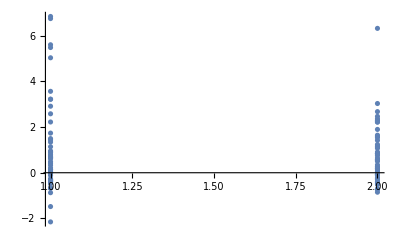
{36.4362,{{{{Symmetric case,{Distance2→{1.27015,5.10591},Distance3→{1.30807,3.13947}}},{Asymmetric case,{Distance2→{0.877762,3.69489},Distance3→{1.18627,2.4768}}}},{{0.127612,2.46897},{1.34267,1.89845},{1.4394,3.03366},{0.0138871,0.528764},{1.49609,0.906357},{-0.475342,0.345151},{0.881044,0.752363},{-0.267838,-0.0634872},{-0.117466,-0.0923979},{-0.418116,-0.219091},{0.713004,0.131705},{5.03745,0.572279},{-2.15446,-0.739879},{1.13867,1.23711},{-1.48208,0.507834},{0.62219,1.6457},{2.22337,0.642956},{2.91478,2.26477},{0.0452896,2.21999},{-0.0114312,-0.513468},{5.48664,1.16809},{0.420204,1.4202},{-0.00312505,-0.0741325},{0.490555,-0.423888},{0.330674,1.12237},{0.21069,0.182655},{0.784971,-0.386661},{-0.385177,-0.476917},{1.73709,2.67752},{5.60792,6.32663},{-0.672824,0.0341578},{-0.373089,-0.279423},{-0.357597,0.190766},{-0.342827,-0.274483},{-0.679135,-0.853204},{6.84841,0.578446},{0.660755,2.22157},{-0.304786,1.53893},{-0.874693,-0.108082},{0.668219,1.59366},{0.951869,0.262441},{-0.327054,1.0709},{2.58332,-0.706021},{6.75526,0.842216},{3.22205,0.830709},{0.136273,0.24981},{0.917245,2.29332},{-0.303847,0.0263473},{3.22205,0.830709},{3.56739,2.36108}}},-Graphics-}}

```mathematica
(Print["Starting pointIdentified process where alpha = ",alpha];
pointIdentified=pointIdentifiedCR[ssSize,numSubsamples,sol[[2]], Cx[noAttr-1], groupIDs, dataArray,method,permuteinvariant,confidenceLevel->(1-alpha),asymptotics->nests, progressUpdate->10];
{pointIdentified,
ListPlot@Flatten[Map[
MapIndexed[Flatten@{#2,#1}&,#]&,
pointIdentified[[-1]]
],1]
})//AbsoluteTiming
```